```mathematica
f[x_] := Sin[x^2]
```

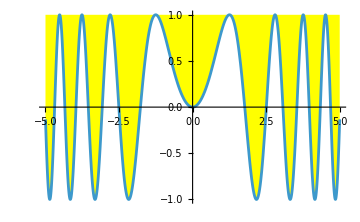

```mathematica
Plot[f[x],{x,-5,5},FillingStyle->Yellow, Filling->Top]
```

```mathematica
Options[Plot];
```

```mathematica
(* Convert f[x] into paramtric function *)
```

```mathematica
S[t_]:={t,f[t]}
```

```mathematica
S[1.5]
```

{1.5,0.778073}

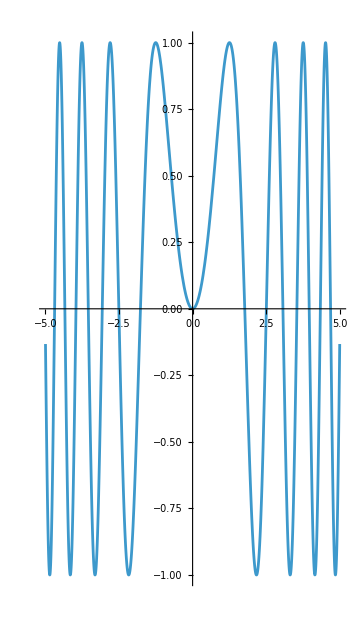

```mathematica
ParametricPlot[S[t],{t,-5,5},AspectRatio->16/9]
```

```mathematica
f1 =#1^2-#2^2&
```

#1^2-#2^2&

```mathematica
(* vector function *)
```

```mathematica
f1[u,v]
```

u^2-v^2

```mathematica
s1[u_,v_]:={u,v,f1[u,v]}
```

```mathematica
s1[1,2]
```

{1,2,-3}

```mathematica
ParametricPlot3D[s1[u,v],{u,-1,1},{v,-1,1}]
```

-Graphics3D-